Coherent state

```mathematica
ϕ[n_,α_]:=ⅇ^(-Abs[α]^2/2)α^n/(√(n!));
```

A useful function of gain

```mathematica
G[g_]:=(√(g^2-1))/g;
```

ACS (not normalized)

```mathematica
Psi[n_,α_,g_]:=ⅇ^(-Abs[G[g]α]^2/2)(1/g-n G[g])ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!));
```

Appropriate value of gain for the condition of zero overlap of ACS with the attenuated coherent state

```mathematica
g0[α_]:=Abs[α]^2/(√(Abs[α]^4-1));
```

Norm of ACS

```mathematica
NormPsi[n_,α_,g_]:=ⅇ^(-Abs[G[g]α]^2/2)√(1/g^2+G[g]^2(Abs[α/g]^2+Abs[α/g]^4)-(2G[g])/g Abs[α/g]^2);
```

Normalized ACS

```mathematica
ψ[n_,α_,g_]:=((1/g-n G[g])ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!)))/(√(1/g^2+G[g]^2(Abs[α/g]^2+Abs[α/g]^4)-(2G[g])/g Abs[α/g]^2));
```

Plot of required value of gain to create ACS as a function of average photon number of the original (unattenuated) coherent state

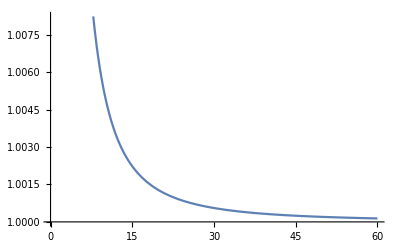

```mathematica
Plot[g0[√navg0],{navg0,2,60},AxesOrigin->{0,1}]
```

Plot of attenuated coherent state and corresponding ACS for different values of average photon number for the original (unattenuated) coherent state

```mathematica
navg0=15;
```

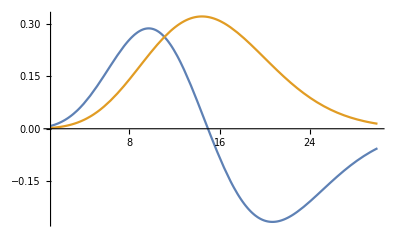

```mathematica
Plot[{ψ[n,√navg0,g0[√navg0]],ϕ[n,(√navg0)/g0[√navg0]]},{n,1,2navg0},PlotRange->Full]
```

Wigner function of coherent state

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ 1/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

(2 ⅇ^(-2 (a^2+b^2)))/π

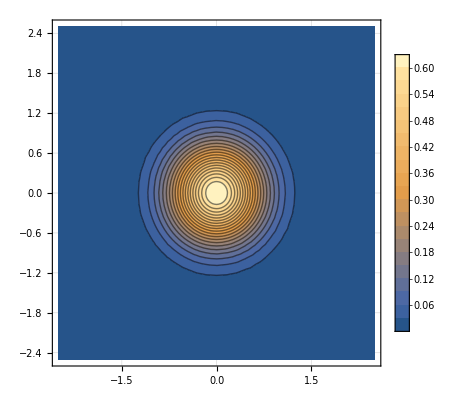

```mathematica
ContourPlot[(2 ⅇ^(-2 (a^2+b^2)))/π,{a,-2.5,2.5},{b,-2.5,2.5},PlotRange->Full,GridLines->Automatic,Contours->20,PlotLegends->Automatic]
```

Wigner function of one photon added coherent state

```mathematica
navg0=5;
Wc1[g_,β_,a_,b_]:=((Abs[2(a+ⅈ b)-β/g]^2-1)/(Abs[β/g]^2+1))(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g]^2))/π;
```

Checking that the integral of the Wigner function gives 1

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ Wc1[g0[√navg0],√navg0,a,b]ⅆaⅆb
```

1

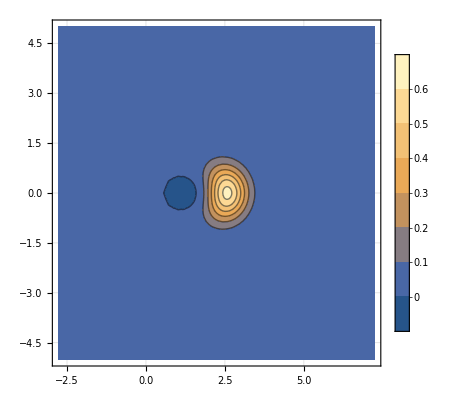

```mathematica
ContourPlot[Wc1[g0[√navg0],√navg0,a,b],{a,√navg0-5,√navg0+5},{b,-5,5},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic]
```

### Plot along the real axis

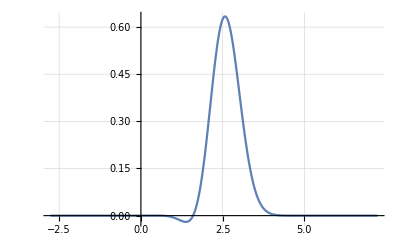

```mathematica
Plot[Wc1[g0[√navg0],√navg0,a,0],{a,√navg0-5,√navg0+5},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic]
```

Calculations to simplify the third term in the Wigner function of ACS

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (x+ⅈ y)/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

(4 (a+ⅈ b) ⅇ^(-2 (a^2+b^2)))/π

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ (x-ⅈ y)/π^2 ⅇ^((x-ⅈ y)(a+ⅈ b)-(x+ⅈ y)(a-ⅈ b)-(x^2+y^2)/2)ⅆxⅆy
```

-(4 (a-ⅈ b) ⅇ^(-2 (a^2+b^2)))/π

Wigner function of ACS

```mathematica
navg0=20;
```

```mathematica
W[g_,β_,a_,b_]:=(1/g^4+G[g]^2(2/g Abs[β/g]^2+Abs[β/g]^2(Abs[2(a+ⅈ b)-β/g]^2-1)-2/g^2(β*(a+ⅈ b)+(a-ⅈ b)β))(2 ⅇ^(-2 Abs[(a+ⅈ b)-β/g]^2))/π)/(1/g^2+G[g]^2(Abs[β/g]^2+Abs[β/g]^4)-(2G[g])/g Abs[β/g]^2);
```

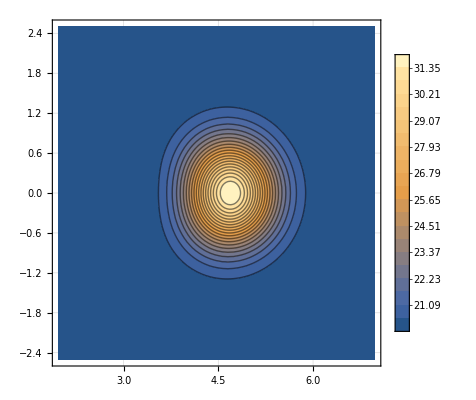

```mathematica
ContourPlot[W[g0[√navg0],√navg0,a,b],{a,√navg0-2.5,√navg0+2.5},{b,-2.5,2.5},PlotRange->Full,PlotLegends->Automatic,GridLines->Automatic,Contours->20]
```

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ W[g0[√navg0],√navg0,a,b]ⅆaⅆb
```

Integrate::idiv: Integral of 159201/160000-(399 ⅇ^(-2 Abs[Times[«2»]+a+Times[«2»]]^2))/(4000 π)+(399 √399 ⅇ^(-2 Abs[«1»]^2))/(40000 π)-(399 a ⅇ^(-2 Abs[Times[«2»]+a+Times[«2»]]^2))/(2000 √5 π)+(399 ⅇ^(-2 Abs[Times[«2»]+a+Times[«2»]]^2) Abs[-(√(399/5))/2+2 a+2 ⅈ b]^2)/(4000 π) does not converge on {-∞,∞}.

∫_(-∞)^∞ ∫_(-∞)^∞ (159201/160000+(ⅇ^(-2 Abs[-(√(399/5))/2+a+ⅈ b]^2) ((399 √399)/200-399/200 (2 √5 (a-ⅈ b)+2 √5 (a+ⅈ b))+399/20 (-1+Abs[-(√(399/5))/2+2 (a+ⅈ b)]^2)))/(200 π))ⅆaⅆb

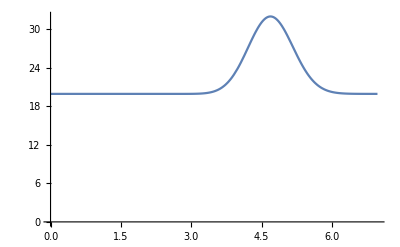

```mathematica
Plot[W[g0[√navg0],√navg0,a,0],{a,0,√navg0+2.5},PlotRange->Full,AxesOrigin->{0,0}]
```